# Mapping of indoor environments with the Wolfram language and Raspberry Pi

## Isaac Ayala

Instituto Tecnológico y de Estudios Superiores de Monterrey

## Project description

The objective is to generate a 2D map of a robot’s environment through the Wolfram language. A robot was built with the purpose of obtaining data, and feeding it to a Raspberry Pi for processing. All of the generated data is then stored in a Woflram Data  Drop bin for analysis.
An example of the pogram’s functionality is shown below.

#### Example image

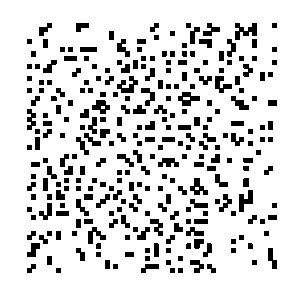
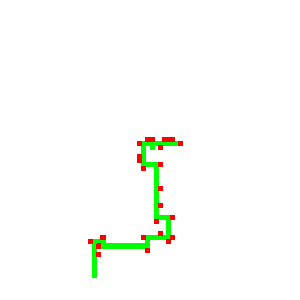
```mathematica
Grid[{{"Map","Discovered surface","Overlay of results"},{-Graphics-,-Graphics-,Overlay[{-Graphics-,-Graphics-}]}},Frame->All]
```

Map | Discovered surface | Overlay of results
-Graphics- | -Graphics- | -Graphics--Graphics-

## Summary of results and conclusions

The algorithm developed has proven capable of generating 2D maps based on inputs obtained from the environment. Results in simulation and in the robot operate under the same principle, registering all information related to movement and collisions in a database (local or online), which can later be processed for further analysis.
Data is obtained by polling sensor information in set intervals, this data is stored alongside a timestamp to calculate the robot’s current position and the new visited areas.

Robot movement is fixed to the four main cardinal directions, and the direction is changed whenever a sensor registers an obstacle that prevents further progress of the robot.
Program execution is halted when the operator chooses. The graphical user interace enables users to control all robot functionality through their computer.

Two operation modes were implemented: scan and control. Scan mode allows autonomous robot operation, whilst control mode obeys the user’s instructions.

## Future directions (optional)

Further development of the algorithm is planned, with the intention of adding new sensors to the robot. New sensors will allow new data to be collected, such as image, distance measurements and